```mathematica
Experiments with the Chua's Circuit

(*
==Chua's circuit==
the double-scroll attractor (sometimes known as Chua's attractor) is a strange attractor observed from a physical electronic chaotic circuit (generally,Chua's circuit) with a single nonlinear resistor (see Chua's Diode).The double-scroll system is often described by a system of three nonlinear ordinary differential equations and a 3-segment piecewise-linear equation (see Chua's equations).This makes the system easily simulated numerically and easily manifested physically due to Chua's circuits' simple design.
-http://www.chuacircuits.com/
-https://en.wikipedia.org/wiki/Multiscroll_attractor
dx/dt=c1*(y-x-f(x)) // m0: slope in outer region
   dy/dt=c2*(x-y+z)    // m1: slope in inner region
   dz/dt=-c3*y         // b: Breakpoints
   f(x)=m1*x+(m0-m1)/2*(|x+1|-|x-1|)
*)
```

```mathematica
hardLim[x_]:=Piecewise[{{0,x>limitValue},{1,x≤limitValue}}]; (* A hard limiter using a piecewise function *)
softLim[x_]:=(1/2)*(Tanh[ (limitValue-x)/softness]+1); (* A soft limiter using a tanh *)

(*Define the chua circuit's differential equations *)
g[x_] := m0 * x + (m1-m0)/2 * (Abs[x+b]-Abs[x-b]);
f[{x_,y_,z_}]:={c1 * (y-x-g[x]),c2*(x-y+z),-c3*y limiter[x] };

(*RK4 Runge Kutta method based on: 
https://en.wikipedia.org/wiki/Runge%E2%80%93Kutta_methods*)
h = 0.001;
RK4 := Module[{y}, 
k1 = h*f[x];
k2 = h*f[x+k1/2];
k3=h*f[x+k2/2];
k4=h*f[x+k3];
y=x+1/6*(k1+2*k2+2*k3+k4);
x = y;
Return[x]];

RK6 := Module[{y}, 
k1 = h*f[x];
k2 = h*f[x+k1/4];
k3=h*f[x+(3.0/32.0)*k1+(9.0/32.0)*k2];
k4=h*f[x+(1932.0/2197.0)*k1-(7200.0/2197.0)*k2
+(7296.0/2197.0)*k3];
k5 = h *f[x+(439.0/216.0)*k1-8.0*k2+(3680.0/513.0)*k3
-(845.0/4104.0)*k4];
k6 = h * f[x-(8.0/27.0)*k1+2.0*k2-(3544.0/2565.0)*k3
+(1859.0/4104.0)*k4-(11.0/40.0)*k5];
y=x+(16.0/135.0)*k1+(6656.0/12825.0)*k3
+(28561.0/56430.0)*k4-(9.0/50.0)*k5+(2.0/55.0)*k6;
x = y;
Return[x]];

x ={-1.5,0,0};
c1=15.6;
c2 =1;
c3 = 28;
m0=-0.714; (*slope in outer region default:-0.714 *)
m1 = -1.143; (*slope in inner region /default: -1.143 *)
b =1; (*Breakpoints *)

limiter = softLim; (* Choose the softlimiter *)
limitValue =4;
	(*For softness 0.13:
1.82 1.83/Period 1 limit cycle (1 to converge) /
2.15/Period 1 limit cycle (high to converge)/
2.183/Period 1 limit cycle (2 to converge)/
2.1995/Period 1 limit cycle (3 to converge)/
2.2/Period 1 limit cycle (4 to converge)/
2.205/Period 1 limit cycle (5 to converge)/
2.206/Period 1 limit cycle (6 to converge)/
2.207/Period 1 limit cycle (7 to converge)/
2.208/Period 1 limit cycle (8 to converge)/
2.209/Period 1 limit cycle (9 to converge)/
2.21/Period 1 limit cycle (10 to converge)/
2.211/Period 1 limit cycle (11 to converge)/

2.215/Period 24 limit cycle/
2.28-2.4 High period limit cycle/Chaos/
2.4-3.19/Chaos/
>3.19/not limited/*)

(* For softness 0.5:
   2.12/ Period 1 limit cycle/
2.25/ Period 2 limit cycle/
2.285/ Period 4 limit cycle/
2.292/ Period 8 limit cycle/
2.2945 /Period 16 limit cycle (?)/
*)
softness = 0.13; (* Softness 0.1 very hard limiter // 0.13 boundary to hard limiter // 0.15 soft limiter  // 1 very soft limiter // 1.88 soft limiter *)

n =150000;
```

```mathematica
limitValue =2.3275;
x ={-1.5,0,0};
chuaPlot=Table[RK6,{i,1,n}]; (* Choose the integration method RK4 or RK6 *)

(* Plot limits*)
limPlot = chuaPlot;

lims = limiter[{chuaPlot[[All,1]]}];
limPlot[[All,3]]= Flatten[Transpose[lims]];

Show[Graphics3D[Point[chuaPlot[[All,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limPlot[[All,3]]]],Graphics3D[Line[chuaPlot[[All,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limPlot[[All,3]]]],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400,BoxRatios->{1,1,1/GoldenRatio}]
```

```mathematica
chuaPlot[[Last,1;;3]]
```

Part::pspec: Part specification Last is neither a machine-sized integer nor a list of machine-sized integers.

{{0.615144,0.215455,0.0112705},{0.619886,0.215865,0.0052395},{0.624645,0.216274,-0.000802846},{0.62942,0.21668,-0.00685645},{0.634213,0.217085,-0.0129212},{0.639023,0.217489,-0.0189972},{0.64385,0.21789,-0.0250842},{0.648694,0.21829,-0.0311823},«149984»,{0.551947,-0.146949,0.233859},{0.550892,-0.146015,0.237957},{0.549849,-0.145079,0.242028},{0.548819,-0.144141,0.246073},{0.547801,-0.143201,0.250092},{0.546795,-0.142259,0.254085},{0.545802,-0.141315,0.258051},{0.544821,-0.140368,0.261991}}⟦Last,1;;3⟧

```mathematica
limitValue = 2.5;
x ={-1.5,0,0};
chuaPlot2=Table[RK6,{i,1,n}]; (* Choose the integration method RK4 or RK6 *)

(* Plot limits*)
limPlot2 = chuaPlot2;

lims2= limiter[{chuaPlot2[[All,1]]}];
limPlot2[[All,3]]= Flatten[Transpose[lims2]];
Show[Graphics3D[Point[chuaPlot2[[All,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limPlot2[[All,3]]]],Graphics3D[Line[chuaPlot2[[All,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limPlot2[[All,3]]]],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400,BoxRatios->{1,1,1/GoldenRatio}]
```

```mathematica
limitValue = 2.28;
x ={-1.5,0,0};
chuaPlot3=Table[RK6,{i,1,n}]; (* Choose the integration method RK4 or RK6 *)

(* Plot limits*)
limPlot3 = chuaPlot3;

lims3= limiter[{chuaPlot3[[All,1]]}];
limPlot3[[All,3]]= Flatten[Transpose[lims3]];
Show[Graphics3D[Point[chuaPlot3[[All,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limPlot3[[All,3]]]],Graphics3D[Line[chuaPlot3[[All,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limPlot3[[All,3]]]],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400,BoxRatios->{1,1,1/GoldenRatio}]
```

```mathematica
limitValue = 2.215;
x ={-1.5,0,0};
chuaPlot4=Table[RK6,{i,1,n}]; (* Choose the integration method RK4 or RK6 *)

(* Plot limits*)
limPlot4 = chuaPlot4;

lims4= limiter[{chuaPlot4[[All,1]]}];
limPlot4[[All,3]]= Flatten[Transpose[lims4]];
chp1=Show[Graphics3D[Point[chuaPlot4[[All,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limPlot4[[All,3]]]],Graphics3D[Line[chuaPlot4[[All,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limPlot4[[All,3]]]],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400,BoxRatios->{1,1,1/GoldenRatio}]

limitValue = 2.211;
x ={-1.5,0,0};
chuaPlot5=Table[RK6,{i,1,n}]; (* Choose the integration method RK4 or RK6 *)

(* Plot limits*)
limPlot5 = chuaPlot5;

lims5= limiter[{chuaPlot5[[All,1]]}];
limPlot5[[All,3]]= Flatten[Transpose[lims3]];
chp2=Show[Graphics3D[Point[chuaPlot5[[All,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limPlot5[[All,3]]]],Graphics3D[Line[chuaPlot5[[All,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limPlot5[[All,3]]]],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400,BoxRatios->{1,1,1/GoldenRatio}]

limitValue = 2.21;
x ={-1.5,0,0};
chuaPlot6=Table[RK6,{i,1,n}]; (* Choose the integration method RK4 or RK6 *)

(* Plot limits*)
limPlot6 = chuaPlot6;

lims6= limiter[{chuaPlot6[[All,1]]}];
limPlot6[[All,3]]= Flatten[Transpose[lims6]];
chp3=Show[Graphics3D[Point[chuaPlot6[[All,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limPlot6[[All,3]]]],Graphics3D[Line[chuaPlot6[[All,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limPlot6[[All,3]]]],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400,BoxRatios->{1,1,1/GoldenRatio}]

limitValue = 2.209;
x ={-1.5,0,0};
chuaPlot7=Table[RK6,{i,1,n}]; (* Choose the integration method RK4 or RK6 *)

(* Plot limits*)
limPlot7 = chuaPlot7;

lims7= limiter[{chuaPlot7[[All,1]]}];
limPlot7[[All,3]]= Flatten[Transpose[lims7]];
chp4=Show[Graphics3D[Point[chuaPlot7[[All,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limPlot7[[All,3]]]],Graphics3D[Line[chuaPlot7[[All,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limPlot7[[All,3]]]],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400,BoxRatios->{1,1,1/GoldenRatio}]

limitValue = 2.208;
x ={-1.5,0,0};
chuaPlot8=Table[RK6,{i,1,n}]; (* Choose the integration method RK4 or RK6 *)

(* Plot limits*)
limPlot8 = chuaPlot8;

lims8= limiter[{chuaPlot8[[All,1]]}];
limPlot8[[All,3]]= Flatten[Transpose[lims8]];
chp5=Show[Graphics3D[Point[chuaPlot8[[All,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limPlot8[[All,3]]]],Graphics3D[Line[chuaPlot8[[All,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limPlot8[[All,3]]]],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400,BoxRatios->{1,1,1/GoldenRatio}]

limitValue = 2.207;
x ={-1.5,0,0};
chuaPlot9=Table[RK6,{i,1,n}]; (* Choose the integration method RK4 or RK6 *)

(* Plot limits*)
limPlot9 = chuaPlot9;

lims9= limiter[{chuaPlot9[[All,1]]}];
limPlot9[[All,3]]= Flatten[Transpose[lims9]];
chp6=Show[Graphics3D[Point[chuaPlot9[[All,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limPlot9[[All,3]]]],Graphics3D[Line[chuaPlot9[[All,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limPlot9[[All,3]]]],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400,BoxRatios->{1,1,1/GoldenRatio}]

limitValue = 2.206;
x ={-1.5,0,0};
chuaPlot10=Table[RK6,{i,1,n}]; (* Choose the integration method RK4 or RK6 *)

(* Plot limits*)
limPlot10 = chuaPlot10;

lims10= limiter[{chuaPlot10[[All,1]]}];
limPlot10[[All,3]]= Flatten[Transpose[lims10]];
chp7=Show[Graphics3D[Point[chuaPlot10[[All,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limPlot10[[All,3]]]],Graphics3D[Line[chuaPlot10[[All,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limPlot10[[All,3]]]],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400,BoxRatios->{1,1,1/GoldenRatio}]

limitValue = 2.205;
x ={-1.5,0,0};
chuaPlot11=Table[RK6,{i,1,n}]; (* Choose the integration method RK4 or RK6 *)

(* Plot limits*)
limPlot11 = chuaPlot11;

lims11= limiter[{chuaPlot11[[All,1]]}];
limPlot11[[All,3]]= Flatten[Transpose[lims11]];
chp8=Show[Graphics3D[Point[chuaPlot11[[All,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limPlot11[[All,3]]]],Graphics3D[Line[chuaPlot11[[All,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limPlot11[[All,3]]]],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400,BoxRatios->{1,1,1/GoldenRatio}]

limitValue = 2.2;
x ={-1.5,0,0};
chuaPlot12=Table[RK6,{i,1,n}]; (* Choose the integration method RK4 or RK6 *)

(* Plot limits*)
limPlot12 = chuaPlot12;

lims12= limiter[{chuaPlot12[[All,1]]}];
limPlot12[[All,3]]= Flatten[Transpose[lims12]];
chp9=Show[Graphics3D[Point[chuaPlot12[[All,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limPlot12[[All,3]]]],Graphics3D[Line[chuaPlot12[[All,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limPlot12[[All,3]]]],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400,BoxRatios->{1,1,1/GoldenRatio}]

limitValue = 2.1995;
x ={-1.5,0,0};
chuaPlot13=Table[RK6,{i,1,n}]; (* Choose the integration method RK4 or RK6 *)

(* Plot limits*)
limPlot13 = chuaPlot13;

lims13= limiter[{chuaPlot13[[All,1]]}];
limPlot13[[All,3]]= Flatten[Transpose[lims13]];
chp10=Show[Graphics3D[Point[chuaPlot13[[All,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limPlot13[[All,3]]]],Graphics3D[Line[chuaPlot13[[All,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limPlot13[[All,3]]]],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400,BoxRatios->{1,1,1/GoldenRatio}]

limitValue = 2.183;
x ={-1.5,0,0};
chuaPlot14=Table[RK6,{i,1,n}]; (* Choose the integration method RK4 or RK6 *)

(* Plot limits*)
limPlot14 = chuaPlot14;

lims14= limiter[{chuaPlot14[[All,1]]}];
limPlot14[[All,3]]= Flatten[Transpose[lims14]];
chp11=Show[Graphics3D[Point[chuaPlot14[[All,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limPlot14[[All,3]]]],Graphics3D[Line[chuaPlot14[[All,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limPlot14[[All,3]]]],Axes->True,AxesLabel->{"x","y","z"},ImageSize->1400,BoxRatios->{1,1,1/GoldenRatio}]

(*GraphicsGrid[{{chp1,chp2},{chp3,chp4},{chp5,chp6},{chp7,chp8},{chp9,chp10},{chp11}}]*)
```

```mathematica
limitValue=3.19;
softLim[2.2417]
```

1.

0.13 Limiter plot

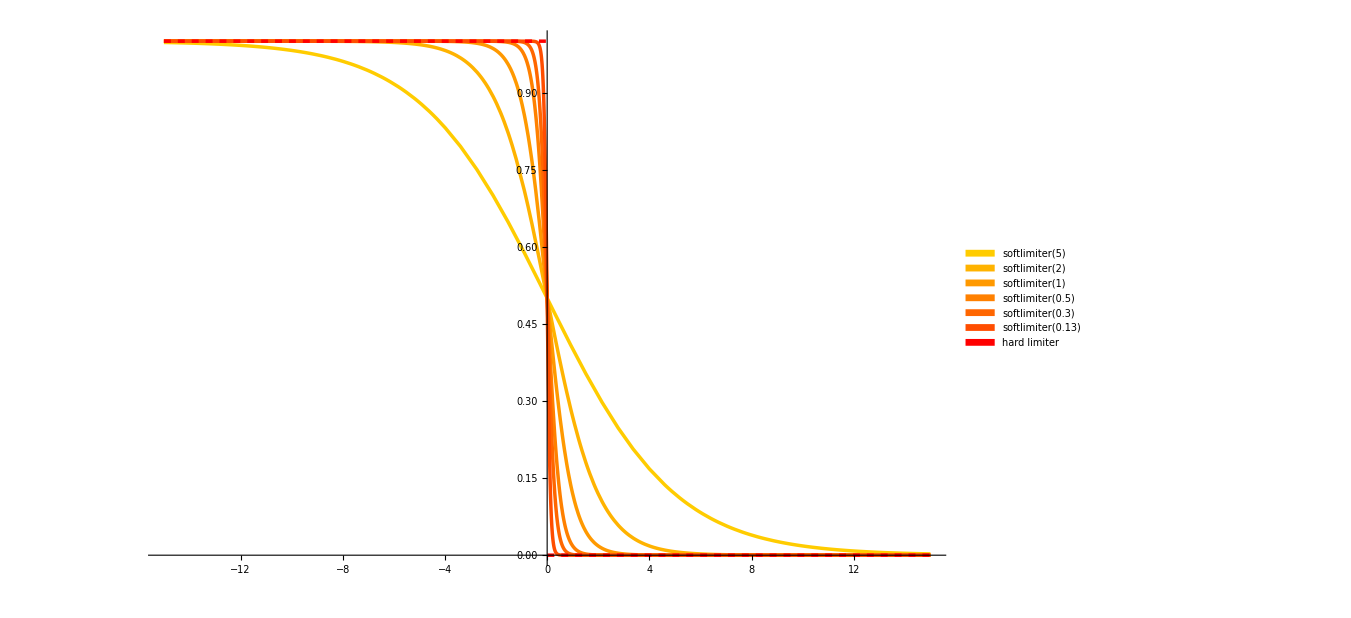

```mathematica
Limiter softness plot
limitValue = 0;

hardLim[x_]:=Piecewise[{{0,x>limitValue},{1,x≤limitValue}}]; (* A hard limiter using a piecewise function *)
softLim[x_,softness_]:=(1/2)*(Tanh[ (limitValue-x)/softness]+1); (* A soft limiter using a tanh *)

lineThickness = 0.0025;
Plot[{softLim[x,5],softLim[x,2],softLim[x,1],softLim[x,0.5],softLim[x,0.3],softLim[x,0.13],hardLim[x]},{x,-15,15},PlotStyle->{
{RGBColor[1,0.8,0],Thickness[lineThickness]},
{RGBColor[1,0.7,0],Thickness[lineThickness]},
{RGBColor[1,0.6,0],Thickness[lineThickness]},
{RGBColor[1,0.5,0],Thickness[lineThickness]},
{RGBColor[1,0.4,0],Thickness[lineThickness]},
{RGBColor[1,0.3,0],Thickness[lineThickness]},
{Red,Dashed,Thickness[lineThickness]}},
PlotLegends->Placed[SwatchLegend[{"softlimiter(5)","softlimiter(2)","softlimiter(1)","softlimiter(0.5)","softlimiter(0.3)","softlimiter(0.13)","hard limiter"},LabelStyle->{GrayLevel[0.3],18}],{0.9,0.5}],ImageSize->1000]
```

```mathematica
Set current working directory to Notebook directory
SetDirectory[NotebookDirectory[]];
```

current directory^2 Notebook Set to working

```mathematica
NotebookDirectory[]
```

/home/leviathan/meta/Work.Repositories/git/minemonics/Minemonics/doc/measurements/